### Vorbereitungen für den Plot

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> White],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)
```

### Mass quantization Plot für verschiedene n

{5,5,5,6,7,8,9,10}

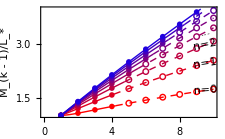

```mathematica
nS = Range[0,7];
nsLabels = "n="<>ToString@#&/@nS;
kRange = Range[1,10]; (* note k=0 is not defined physically *)
colors=Blend[{Red,Blue},#/Length@nS]&/@nS;
(*colors = {Red,Blue,Darker@Green, Darker@Yellow,Green,Darker@Blue,Darker@Red,Magenta,Darker@Magenta}; *)(* minLength@colors ≥ Length@nS *)
Ms[k_,n_]=1/2(k+1)/k^(1/(n+2));
rk[k_,n_] = k^(1/(2+n));
(* analytischer Ausdruck aus thermodynamik-rechnungen.nb *)
rC[n_] =2^(1/(2+n)) (-4-3 n-n^2+(2+n) √(5+2 n+n^2))^(-1/(2+n));
(* rC nimmt diese Werte an:  {2.06,1.60,1.48,1.41, 1.36,1.33,1.30,1.28}; *)
maxQuantumK=1+Total@Table[If[rk[k,#]≤ rC[#],1,0],{k,kRange}]&/@ nS
fig=Show[
Plot[
Evaluate@Flatten[{
If[rk[k,#]≤ rC[#],Ms[k,#],],
If[rk[k,#]≥ rC[#],Ms[k,#],]
}&/@nS],
{k,First@kRange,Last@kRange},
PlotRange-> {{0,Last@kRange},{1,4} },
PlotRangeClipping->True,
PlotStyle-> Flatten[{#,{Dashed,#}}&/@colors,1],
(*PlotLegends->nS,*)
Epilog-> {
EpiLabels[9.5, Ms[X,#]&/@nS⟦1;;4⟧, {"n=0","n=1","n=2","..."}]
},
ImageSize-> 8cm,
Frame-> True,
FrameLabel-> {"k","M_(k - 1)/L_*"},
PlotRangePadding->None
],
Graphics@
Table[
Module[{n=#1⟦1⟧, color=#1⟦2⟧,  quantK=#1⟦3⟧,Mc,form,output},
form = If[k ≥ quantK, Circle[], Disk[]];
output = Inset[Graphics@{color, form},{k,Ms[k,n]}, Center, 0.25]
]&/@ Transpose@{nS,colors,maxQuantumK },
{k,kRange}
]~Flatten~1
]
```

```mathematica
Export["../figures/mass-quantization-linear.pdf",Show@fig]
```

../figures/mass-quantization-linear.pdf

### Anders skaliert

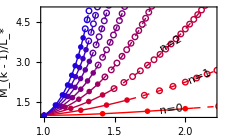

```mathematica
kfromR[r_,n_] = r^(2+n);
kRange2 = Range[1,30];
fig2=Show[
Plot[
Evaluate@Flatten[
With[{k=kfromR[r,#]},
{
If[rk[k,#]≤ rC[#],Ms[k,#],],
If[rk[k,#]≥ rC[#],Ms[k,#],]
}
]&/@nS],
{r,1,2.2},
PlotRange-> {1,5},
PlotRangeClipping->True,
PlotStyle-> Flatten[{#,{Dashed,#}}&/@colors,1],
(*PlotLegends->nS,*)
Epilog-> {
EpiLabels[{1.9,2.1,1.9,1.7}, Ms[kfromR[X,#],#]&/@nS⟦1;;4⟧, {"n=0","n=1","n=2","..."},2.7]
},
ImageSize-> 8cm,
Frame-> True,
FrameLabel-> {"r_H/L_*","M_(k - 1)/L_*"},
PlotRangePadding->None
],
Graphics@
Table[
Module[{n=#1⟦1⟧, color=#1⟦2⟧,  quantK=#1⟦3⟧,Mc,form,output},
form = If[k ≥ quantK, Circle[], Disk[]];
output = Inset[Graphics@{color, form},{rk[k,n],Ms[k,n]}, Center, 0.03]
]&/@ Transpose@{nS,colors,maxQuantumK },
{k,kRange2}
]~Flatten~1
]
```

```mathematica
Export["../figures/mass-quantization.pdf",Show@fig2]
```

../figures/mass-quantization.pdf

### Rechungen zu den Limité

```mathematica
M[n_] = 1/2 (n^(1/2)+n^(-1/2))
```

1/2 (1/(√n)+√n)

```mathematica
M[n+1]-M[n] // FullSimplify
```

1/2 (-1/(√n)-√n+(2+n)/(√(1+n)))

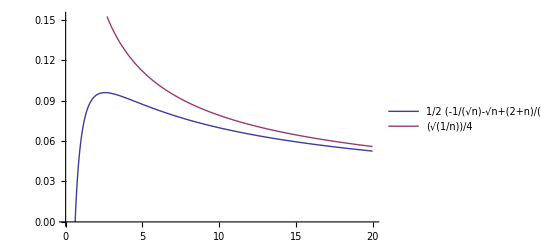

```mathematica
Plot[Evaluate@{1/2 (-1/(√n)-√n+(2+n)/(√(1+n))),(√(1/n))/4},{n,0,20},PlotLegends-> "Expressions"]
```

```mathematica
Series[1/2 (-1/(√n)-√n+(2+n)/(√(1+n))),{n,∞,3}]
```

(√(1/n))/4-5/16 (1/n)^(3/2)+7/32 (1/n)^(5/2)+O[1/n]^(7/2)

```mathematica
M2[k_]=1/(n+2)(k+1)/k^(1/(n+2))
```

(k^(-1/(2+n)) (1+k))/(2+n)

```mathematica
M2[k+1]-M2[k] // FullSimplify
```

(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n)

```mathematica
ser=Series[
Table[(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n),{n,0,3}],{k,∞,3}] //TableForm
```

(√(1/k))/4-5/16 (1/k)^(3/2)+7/32 (1/k)^(5/2)+O[1/k]^(7/2)
2/9 (1/k)^(1/3)-4/27 (1/k)^(4/3)+22/243 (1/k)^(7/3)+O[1/k]^(10/3)
3/16 (1/k)^(1/4)-11/128 (1/k)^(5/4)+25/512 (1/k)^(9/4)+O[1/k]^(13/4)
4/25 (1/k)^(1/5)-7/125 (1/k)^(6/5)+19/625 (1/k)^(11/5)+O[1/k]^(16/5)

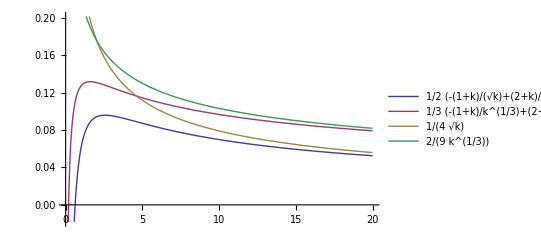

```mathematica
Plot[
Evaluate@Join[
Table[(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n),{n,0,1}],
Table[(1+n)/((2+n)^2 k^(1/(2+n))),{n,0,1}]
],
{k,0,20},
PlotLegends-> "Expressions"
]
```

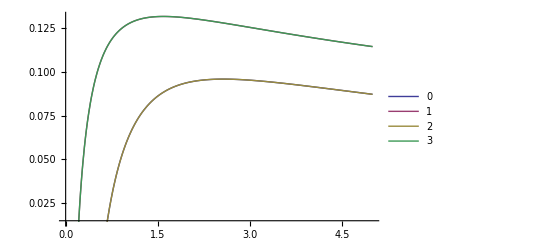

```mathematica
Plot[Evaluate@Join[
Table[(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n),{n,0,1}],
Table[(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n),{n,0,1}]
],
{k,0,5},PlotLegends-> {0,1,2,3,0,1,2,3}]
```

```mathematica
k^(-1/(2+n)) (1+k)^(-1/(2+n)) ((1+k)^(1/(2+n)) (-k/(2+n)-1/(2+n)+O[1/k]^11)+k^(1/(2+n)) (k/(2+n)+2/(2+n)+O[1/k]^11))//Normal
```

k^(-1/(2+n)) (1+k)^(-1/(2+n)) ((1+k)^(1/(2+n)) (-1/(2+n)-k/(2+n))+k^(1/(2+n)) (2/(2+n)+k/(2+n)))

```mathematica
k^(-1/(2+n)) (1+k)^(-1/(2+n)) ((1+k)^(1/(2+n)) (-1/(2+n)-k/(2+n))+k^(1/(2+n)) (2/(2+n)+k/(2+n)))//FullSimplify
```

(-k^(-1/(2+n)) (1+k)+(1+k)^(-1/(2+n)) (2+k))/(2+n)